```mathematica
SetDirectory[NotebookDirectory[]];ClearAll["Global`*"];
Get["../sources/KimberlingPoints.m"];
Get["../sources/TriangleTools.m"];
Get["../db/ETC.mx"];
Get["../db/ETCBaryNorm.mx"];
Get["../db/TriangleCurves.mx"];
Get["../db/CentralCircles.mx"];
Get["../db/KimberlingTrianglesBary.mx"];
Get["../db/KimberlingTrianglesBaryOrthKeys.mx"];
Get["../sources/fltCircles.m"];
Get["../sources/TriangleCurves.m"];
Get["../sources/TriangleExpressions.m"];
Get["../sources/DBTools.m"];
Get["../db/CPTR.mx"];
Get["../db/UNCFTRG.mx"];
Get["../db/ENCTR.mx"];
PA={31/3,(4 √35)/3}; PB={0,0}; PC={6,0};
xA={1,0,0}; xB={0,1,0}; xC={0,0,1}; pP={u,v,w};pQ={p,q,r};
sr=simplifyRationalBarycentrics;
(* Add Extra points to ETC*)
ETCFull=ETC;
ETCBaryNormFull=ETCBaryNorm;
Get["../db/NonETCNames.mx"];
```

```mathematica
loadedData = Import["../db/precomputed_triangles.mx"];
 precomputedKimberling = loadedData["Kimberling"];
precomputedCPTR = loadedData["CPTR"];
precomputedENCTR = loadedData["ENCTR"];
precomputedUNCFTRG = loadedData["UNCFTRG"];
allPrecomputedTrJoined=Join[precomputedKimberling,precomputedCPTR,precomputedENCTR,precomputedUNCFTRG];
```

```mathematica
Get["../db/ETCExtra.mx"];
Get["../db/ETCExtraBary.mx"];

Do[
AppendTo[ETCFull,ptname->ETCExtra[ptname]];
AppendTo[ETCBaryNormFull,ptname->ETCExtraBary[ptname]];
,{ptname,Keys[ETCExtra]}
];

colorPrintOn=True;
```

```mathematica
Get["../db/ETCExtra.mx"];
Get["../db/ETCExtraBary.mx"];

Do[
AppendTo[ETC,ptname->ETCExtra[ptname]];
AppendTo[ETCBaryNorm,ptname->ETCExtraBary[ptname]];
,{ptname,Keys[ETCExtra]}
];

ETCFull=ETC;
ETCBaryNormFull=ETCBaryNorm;

colorPrintOn=True;
```

```mathematica
Max[ToExpression[StringTake[Keys[KeySelect[ETC,StringStartsQ[#,"X"]&]],{2,-1}]]]
```

72421

```mathematica
Take[NonETCNames,-1]
```

<|Z93434→IsogConj(X65148)|>

```mathematica
ToExpression[StringTake[#,{11,-2}]]&/@Select[NonETCNames,StringStartsQ[#,"IsogConj"]&]//Max
```

65148

Not good for expressions, does not Factor

```mathematica
multiCollectABC[pt_]:=PolynomialForm[#,TraditionalOrder->True]&/@{Collect[pt[[1]],a_,Simplify],Collect[pt[[2]],b_,Simplify],Collect[pt[[3]],c_,Simplify]}
```

```mathematica
Do[If[Not[NumericQ[evaluate[ex]/.rule69]],Print[ex]],{ex,exprs}]
```

```mathematica
Select[Take[ETC,{1,2000}],polynomialDegree[simplifyRationalBarycentrics[#//symmetrizeInternal2][[1]]]==2&]
```

```mathematica
Select[Keys[KimberlingTrianglesBary],StringContainsQ[#,"Hung"]&]
```

{Hung-Feuerbach,Montesdeoca-Hung,Moses-Hung}

Extraversions?

```mathematica
ea=KimberlingCenterCN[24]/.Thread[{a,b,c}->{-a,b,c}]//simplifyRationalBarycentrics
eb=KimberlingCenterCN[24]/.Thread[{a,b,c}->{a,-b,c}]//simplifyRationalBarycentrics
ec=KimberlingCenterCN[24]/.Thread[{a,b,c}->{a,b,-c}]//simplifyRationalBarycentrics
```

```mathematica
ptcoord=bReflectionPL[X[7],bLine[X[1],X[4]]];
```

```mathematica
singlePointProcesses=Association[
"complement"->{v+w,u+w,u+v},
"anticomplement"->{-u+v+w,u-v+w,u+v-w}
];
```

```mathematica
globalNoCleanup=False;globalOutputStream=False;globalSilence=False;colorPrintOn=False;globalCheckAllPoles=False;
```

```mathematica
globalSeenPoints=List[];globalProperties=Association[];
```

```mathematica
pointChecker[ptcoord,0,True,"XX"];
```

Starting...

X(7)X(522)∩X(4)X(2405)

Barycentrics    (a+b-c)*(a-b+c)*(a^2+(b-c)^2-2*a*(b+c))^(-1)*(a^6-a^5*(b+c)+2*a^3*(b-c)^2*(b+c)-a*(b-c)^4*(b+c)-a^4*(b^2-3*b*c+c^2)+(b^2-c^2)^2*(b^2-b*c+c^2)-a^2*(b-c)^2*(b^2+4*b*c+c^2))^(-1)*(a^6-a^5*(b+c)-4*a^3*(b-c)^2*(b+c)-3*a*(b-c)^2*(b+c)^3+5*a^2*(b^2-c^2)^2+a^4*(b^2-b*c+c^2)+(b^2-c^2)^2*(b^2+b*c+c^2))

Lies on these lines: {2, 67470}, {4, 2405}, {7, 522}, {8, 24029}, {390, 515}, {653, 1360}, {938, 18339}, {1785, 10590}, {2002, 10538}, {3085, 67467}, {3319, 3476}, {3600, 67725}, {3616, 67469}, {4313, 67464}, {4552, 20344}, {5218, 60062}, {5226, 61732}, {5261, 51889}, {5435, 67628}, {5603, 39546}, {5703, 31866}, {7179, 69459}, {8232, 67462}, {9779, 67463}, {10578, 67468}

= {X(i),X(j)}-harmonic conjugate of X(k) for these (i,j,k): {522, 67461, 7}

= reflection of X(i) in X(j) for these {i,j}: {7, 67461}

= reflection of X(i) in line X(j)X(k) for these {i,j,k}: {7, 1, 4}, {390, 1, 1459}

68.157039

Starting circumconics

7.5227083

Starting curves

$Aborted

```mathematica
printGlobalProperties[globalProperties,"XX","XX"]
```

XX = X(7)X(522)∩X(4)X(2405)

Barycentrics    (a+b-c)*(a-b+c)*(a^2+(b-c)^2-2*a*(b+c))^(-1)*(a^6-a^5*(b+c)+2*a^3*(b-c)^2*(b+c)-a*(b-c)^4*(b+c)-a^4*(b^2-3*b*c+c^2)+(b^2-c^2)^2*(b^2-b*c+c^2)-a^2*(b-c)^2*(b^2+4*b*c+c^2))^(-1)*(a^6-a^5*(b+c)-4*a^3*(b-c)^2*(b+c)-3*a*(b-c)^2*(b+c)^3+5*a^2*(b^2-c^2)^2+a^4*(b^2-b*c+c^2)+(b^2-c^2)^2*(b^2+b*c+c^2))

XX lies on these lines: {2, 67470}, {4, 2405}, {7, 522}, {8, 24029}, {390, 515}, {653, 1360}, {938, 18339}, {1785, 10590}, {2002, 10538}, {3085, 67467}, {3319, 3476}, {3600, 67725}, {3616, 67469}, {4313, 67464}, {4552, 20344}, {5218, 60062}, {5226, 61732}, {5261, 51889}, {5435, 67628}, {5603, 39546}, {5703, 31866}, {7179, 69459}, {8232, 67462}, {9779, 67463}, {10578, 67468}

XX = reflection of X(i) in X(j) for these {i,j}: {7, 67461}

XX = reflection of X(i) in line X(j)X(k) for these {i,j,k}: {7, 1, 4}, {390, 1, 1459}

StringRiffle::list: List expected at position 1 in StringRiffle[Missing[KeyAbsent,curves],, ].

StringJoin::string: String expected at position 2 in XX lies on these curves: <>StringRiffle[Missing[KeyAbsent,curves],, ].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[XX lies on these curves: <>StringRiffle[Missing[KeyAbsent,curves],, ],RegularExpression[[, ]*{+([Y|Z]*?[\d, \(\)ABCX])*[Y|Z].*?}+]→].

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[StringReplace[XX lies on these curves: <>StringRiffle[Missing[KeyAbsent,curves],, ],RegularExpression[[, ]*{+([Y|Z]*?[\d, \(\)ABCX])*[Y|Z].*?}+]→],KeyAbsent].

```mathematica
(*Check if any point of bary array is in ETC*)
Monitor[Do[
check = checkPointinETC2[symmetrizeInternal[t]];
If[Length[check]>0,Print[t];Print[check]];
,{t,test}
],t]
```

```mathematica
res=Select[StringReplace[#,{"("->"",")"->""}]&/@Out[422],Not[StringStartsQ[#,"X"]]&]
```

```mathematica
(* Double Expression Checker for the Big List*)
out={};Do[
If [mx==nx||Max[mx,nx]<=12, Continue[]];
check = checkPointinETC2[E9868[X[nx],X[mx]]];
If[Length[check]>0,
Print[{nx,mx}];AppendTo[out,{nx,mx,check[[1]]}];
];
,{nx,1,21},{mx,1,21}];
Print[out];
```

```mathematica
(* Fuzzy membership check 
baryset - List of barycentrics
set - list of points to replace in replacer[]
expr - expression being tested
*)
```

```mathematica
out={};
intbaryset = intnumericnorm/@ReplaceAll[symmetrizeInternal/@baryset,rule69];
Do[
check=replacer[expr,ptn]/.rule69//intnumericnorm;
If[
Length[Select[intbaryset,Abs[#[[1]]-check[[1]]]<10^-10&]]>0,
Print[ptn];AppendTo[out,ptn];
]
,{ptn,set}
];
```

```mathematica
(*Conversion to remove trigs from barys*)
$Assumptions=a>0&&b>0&&c>0&&S>0;
tst=multiCollectFactors[#,S]&/@(-(ETC["X55420"]//evaluate//Simplify)/.(1-((-a^2+b^2+c^2)^2)/(4 b^2 c^2)->S^2/(b^2 c^2))//symmetrizeInternal//simplifyRationalBarycentrics//simplifyRationalBarycentrics//simplifyRationalBarycentrics)
$Assumptions=True;
```

{a (2 b^2 c^2+(a^2-(b+c)^2) S),b (2 a^2 c^2+(-a^2+b^2-2 a c-c^2) S),c (2 a^2 b^2+(-a^2-2 a b-b^2+c^2) S)}

From Trilinear expression to Barycentric expression

```mathematica
-bFromTrilinear[f[sym3[Cos[A]],bIsotomicConjugate[{x,y,z}]]]/.Thread[{x,y,z}->bToTril[{x,y,z}]]//simplifyRationalBarycentrics//simplifyRationalBarycentrics
```

{a (a y z Cos[A]-x (b z Cos[B]+c y Cos[C])),b (-a y z Cos[A]+b x z Cos[B]-c x y Cos[C]),c (-a y z Cos[A]-b x z Cos[B]+c x y Cos[C])}

```mathematica
(* Check Y/Z points on cubics *)
NonETCNames/@(checkPointsOnCurve[getTriangleCurve["K051"]]//Quiet//setRemoveBrackets);
Select[%,Not[MissingQ[#]]&]//Print
```

```mathematica
(* Check points on cubics *)
Do[ptcoord=bCrossConjugate[X[2],X[nx]];
l=ptcoord//checkCurves//Quiet;If[Length[l]>0,Print[nx];Print[checkPointinETC2[ptcoord]]],{nx,31,1000}]
```

```mathematica
AbsoluteTiming[
tretc=Table[{idx,N[NormalizeBary[evaluate[bCoordChangeK[idx,##]&@@tr]/.rule69],24]},{idx,1,3000}];
]//Quiet
```

{7.98305,Null}

Mass quick checker

```mathematica
expr=sym3[p u (r v+q w) (p r^2 u v^2+p q^2 u w^2+q v (r^2 u^2-4 p r u w+p^2 w^2)) (q^2 r u^2 w+p^2 r v^2 w+p u (r^2 v^2-4 q r v w+q^2 w^2))];
out={};
Do[
If[in==2,Continue[]];
Print[{in,im}];
ptcoord=replacer[expr,in,im]//simplifyRationalBarycentrics;
tot=quickChecker[ptcoord,0,True]//Total;
crvsnum=checkCurves[ptcoord]//Quiet//Length;
If[tot+10*crvsnum>10,AppendTo[out,{in,im}];Print[out]];
,{in,1,12},{im,Max[3,in+1],12}]
```

{1,3}

(name pending)

Barycentrics    a^2*(a+b-c)*(a-b+c)*(b+c)*(a^2-b^2-c^2)*(a^6*c+b^2*(b-c)^3*c*(b+c)-a^5*(b^2-2*b*c+3*c^2)+2*a^3*c*(-b^3+2*b^2*c-2*b*c^2+c^3)+a^4*(2*b^3-3*b^2*c+2*c^3)+a*(b-c)^2*(b^4+2*b^3*c+4*b^2*c^2+4*b*c^3+c^4)+a^2*(-2*b^5+b^4*c+4*b^2*c^3-3*c^5))*(a^6*b-b*(b-c)^3*c^2*(b+c)-a^5*(3*b^2-2*b*c+c^2)+2*a^3*b*(b^3-2*b^2*c+2*b*c^2-c^3)+a^4*(2*b^3-3*b*c^2+2*c^3)+a*(b-c)^2*(b^4+4*b^3*c+4*b^2*c^2+2*b*c^3+c^4)+a^2*(-3*b^5+4*b^3*c^2+b*c^4-2*c^5))

Lies on these lines: {243, 2639}

= intersection, other than A, B, C, of circumconics: {{A, B, C, X(21), X(73)}}

{1,4}

(name pending)

Barycentrics    a*(a+b-c)*(a-b+c)*(b+c)*(a^6*c+b^2*(b-c)^3*c*(b+c)-a^5*(b^2-2*b*c+3*c^2)+2*a^3*c*(-b^3+2*b^2*c-2*b*c^2+c^3)+a^4*(2*b^3-3*b^2*c+2*c^3)+a*(b-c)^2*(b^4+2*b^3*c+4*b^2*c^2+4*b*c^3+c^4)+a^2*(-2*b^5+b^4*c+4*b^2*c^3-3*c^5))*(a^6*b-b*(b-c)^3*c^2*(b+c)-a^5*(3*b^2-2*b*c+c^2)+2*a^3*b*(b^3-2*b^2*c+2*b*c^2-c^3)+a^4*(2*b^3-3*b*c^2+2*c^3)+a*(b-c)^2*(b^4+4*b^3*c+4*b^2*c^2+2*b*c^3+c^4)+a^2*(-3*b^5+4*b^3*c^2+b*c^4-2*c^5))

Lies on these lines: {1936, 9358}

$Aborted

```mathematica
expr=sym3[u+Cos[C]v+Cos[B]w];
out={};
Do[
If[in==2,Continue[]];
Print[in];
ptcoord=simplifyRationalBarycentrics[expr/.Thread[pP->KimberlingCenterC[in]]];tot=quickChecker[ptcoord]//Total;
If[tot>10,AppendTo[out,in];Print[out]];
,{in,1,120}]
```

Triangles on curves

```mathematica
ecrv=crv/.rule69//curveSimplify;
```

```mathematica
Select[Table[{nx,(ecrv/.Thread[{x,y,z}->(evaluate[bCircumcevianTriangle[X[nx]][[1]]]/.rule69)])},{nx,1,3000}],#[[2]]==0&]
```

{}

```mathematica
(*duplicate triangle checker*)
Do[
If[
Length[checkTriangleExists2[CPTR[key]]]>1,
Print[key];KeyDropFrom[CPTR,key]
];
,{key,Keys[KeySelect[CPTR,StringStartsQ[#,"pedal"]&]]}
];
```

$Aborted

```mathematica
(*degenerate triangle checker*)
CPTR2=CPTR;
i=0;Do[
i=i+1;If[Mod[i,20]==1,Print[i]];
res=Timing[Abs[((CPTR2[trg][[1]]/.rule69)-(CPTR2[trg][[2]]/.rule69)//Simplify)]];
If[res[[1]]>2,Print["CHECK: "<>trg]];
If[Total[Abs[res[[2]]]]<10^-24,Print[trg];KeyDropFrom[CPTR,trg]];

res=Timing[Abs[((CPTR2[trg][[1]]/.rule69)+(CPTR2[trg][[2]]/.rule69)//Simplify)]];
If[res[[1]]>2,Print["CHECK: "<>trg]];
If[Total[Abs[res[[2]]]]<10^-24,Print[trg];KeyDropFrom[CPTR,trg]];

,{trg,Keys[CPTR2]}]
```

Check for squared expressions

```mathematica
Monitor[
Do[
fl=Table[fct[[2]],{fct,FactorList[replacerExprNoeval[(u^4+v^2 w^2+2 u^3 (v+w)+2 u v w (v+w)+2 u^2 (v^2+v w+w^2)),idx]]}];
If[Length[Select[fl,OddQ[#]&]]<=1, Print[idx]]
,{idx,601,800}],
idx
]
```

Variable elimination

```mathematica
expr=-12 a^8+8 a^6 (b^2+c^2)-a^4 (-13 b^4+22 b^2 c^2-13 c^4)-(b^2-c^2)^2 (3 b^4-2 b^2 c^2+3 c^4)-2 a^2 (5 b^6-3 b^4 c^2-3 b^2 c^4+5 c^6);
```

```mathematica
Eliminate[{f==expr,
a^2+b^2-c^2==2 SC,a^2-b^2+c^2==2 SB,-a^2+b^2+c^2==2 SA,-a^4+2 a^2 b^2-b^4+2 a^2 c^2+2 b^2 c^2-c^4==4 S^2
},{a,b,c}
]//Factor//Simplify
```

f==-4 (3 S^4+SB^4+31 SB^2 SC^2-6 SB SC^3+SC^2 (6 SA^2-6 SA SC+SC^2)+2 S^2 (SA^2+SB^2-3 SA SC-12 SB SC+4 SC^2))&&S^2==SB SC+SA (SB+SC)

```mathematica
Simplify[expr,-a^4+2 a^2 b^2-b^4+2 a^2 c^2+2 b^2 c^2-c^4==4 S^2]
```

-12 a^8+8 a^6 (b^2+c^2)-(b^2-c^2)^2 (3 b^4-2 b^2 c^2+3 c^4)+a^4 (13 b^4-22 b^2 c^2+13 c^4)-2 a^2 (5 b^6-3 b^4 c^2-3 b^2 c^4+5 c^6)

Sorting global, dropping keys, renumbering

```mathematica
BASEPATH = "C:\\Users\\ivan.pavlov\\Documents\\Wolfram Mathematica\\var\\";
```

```mathematica
Get[BASEPATH<>"globalptnames.mx"]
Get[BASEPATH<>"globalptdescr.mx"];
Get[BASEPATH<>"globalptexpr.mx"];
Get[BASEPATH<>"globalptbary.mx"];
```

```mathematica
Table[pt[[1]],{pt,Values[globalptbary]}]//DuplicateFreeQ(*Tally, DuplicateFreeQ*)
```

True

```mathematica
out=<|//;
Do[
AssociateTo[out,name->{name,globalptdescr[name]}];
,{name,Keys[globalptnames]}
];
Length[out]
out=ReverseSortBy[out,#[[2]]&];
```

815

```mathematica
(*Selective filtering*)
Num=70;tot=0;Do[
ln=Map[#[[1]]&,
Select[Values[out],
StringContainsQ[globalptnames[[#[[1]]]],"CTR28-"<>ToString[i]]&&(
(#[[2]]>Num)||
(MemberQ[{3,20,253,264,329},i]&&#[[2]]>14&&StringContainsQ[globalptnames[[#[[1]]]],"CTR28-"<>ToString[i] ])
)
&
]];
tot += Length[ln];
Print[Length[ln]];
,{i,{1,2,3,4,6,7,8,9,20,69,95,189,253,264,329}}
]; Print[tot];
```

13

73

14

26

18

45

17

0

10

18

0

9

33

1

8

285

```mathematica
key=Map[#[[1]]&,Select[Values[out],
(
#[[2]]>=100
||
(
Not[StringContainsQ[globalptnames[[#[[1]]]],"pedal"] ] &&
Not[StringContainsQ[globalptnames[[#[[1]]]],"cevian"] ]&& 
Not[StringContainsQ[globalptnames[[#[[1]]]],"UCFT"] ]&& 
StringCount[globalptnames[[#[[1]]]],"CTR"]==1&&
#[[2]]>=30
)
)
&
]
]//Sort;
(*key=Table["X"<>ToString[nn],{nn,70380,70395}]*)
(*key=Map[#[[1]]&,Select[Values[out],And[#[[2]]>100,Length[checkPointinETC2[sym[globalptexpr[#[[1]]]]]]>0]&]]*)
```

```mathematica
keysToDrop = Complement[Keys[globalptnames],Union[key,{"X80000","X80001","X80002","X80021","X80322","X80325","X80330","X80336","X80343",
"X80391","X80392","X80393","X80396","X80400","X80401","X80405","X80406","X80407","X80408","X80410","X80414","X80415","X80418","X80419","X80420","X80421","X80422","X80423","X80424","X80425","X80426","X80523","X80525","X80527","X80528","X80529","X80530","X80534","X80599","X80600","X80643","X80644","X80645","X80723","X80724","X80757","X80775","X80799","X80800"}]]
```

```mathematica
KeyDropFrom[globalptnames,keysToDrop];
KeyDropFrom[globalptdescr,keysToDrop];
KeyDropFrom[globalptexpr,keysToDrop];KeyDropFrom[globalptbary,keysToDrop];
```

```mathematica
start=80000;
globalptnames1=Association[];
globalptdescr1=Association[];
globalptexpr1=Association[];
globalptbary1=Association[];
Do[
newname="X"<>ToString[start];
AssociateTo[globalptnames1,newname->globalptnames[name]];
AssociateTo[globalptdescr1,newname->globalptdescr[name]];
AssociateTo[globalptexpr1,newname->globalptexpr[name]];
AssociateTo[globalptbary1,newname->globalptbary[name]];
start=start+1;
,{name,Keys[globalptnames]}
];
```

```mathematica
globalptnames=globalptnames1;
globalptdescr=globalptdescr1;
globalptexpr=globalptexpr1;
globalptbary=globalptbary1;
DumpSave["globalptnames.mx",globalptnames];
DumpSave["globalptdescr.mx",globalptdescr];
DumpSave["globalptexpr.mx",globalptexpr];
DumpSave["globalptbary.mx",globalptbary];
```

Cleanup of known points

```mathematica
checkPointinETC2[ptnum_]:=Module[{set,out,cmplx},
If[AllTrue[ptnum,Im[#1]==0&],set=Keys[Select[ETCBaryNorm,#1==ptnum&]],cmplx=Keys[Select[ETCBaryNorm,AnyTrue[#1,Im[#1]≠0&]&]];set=Select[cmplx,coincide[ETCBaryNorm[#1],ptnum]&];];out={};Return[Length[set]>0];
];
```

```mathematica
Do[
name="X"<>ToString[idx];
If[checkPointinETC2[globalptbary[name]],
Print[name];
KeyDropFrom[globalptnames,name];KeyDropFrom[globalptdescr,name];KeyDropFrom[globalptexpr,name];KeyDropFrom[globalptbary,name];
];
If[Mod[idx,100]==0,Print["Reached "<>name]]
,{idx,70000,70216}]
```

Reached X70000

Reached X70100

Reached X70200

```mathematica
Do[
If[heuristicsCheck[ETCExtra[ptname]],
Print[ptname<>": "<>NonETCNames[ptname]]];
,{ptname,Take[Keys[Select[NonETCNames,StringStartsQ[#,"CM1"]&]],100]}
];
```

EXPRESSIONS

```mathematica
Simplify[Cot[A]-(-a^2+b^2+c^2)/(2S)//evaluate,rulesSimplify]
```

0

```mathematica
2(S^2)/(sa)//evaluate//Expand
```

a^3+a^2 b-a b^2-b^3+a^2 c+2 a b c+b^2 c-a c^2+b c^2-c^3

```mathematica
-2S(2r+R)//evaluate//Together
```

a^3-a^2 b-a b^2+b^3-a^2 c+a b c-b^2 c-a c^2-b c^2+c^3

```mathematica
2S(R-2r)//evaluate//Together
```

a^3-a^2 b-a b^2+b^3-a^2 c+3 a b c-b^2 c-a c^2-b c^2+c^3

```mathematica
(-4S(4R+r))/(a+b+c)//evaluate//Simplify//Expand
```

a^2-2 a b+b^2-2 a c-2 b c+c^2

```mathematica
16 r^2 sp^2 (2 r^2+8 r R+9 R^2-2 sp^2)//evaluate//Simplify//Expand
```

a^6-a^4 b^2-a^2 b^4+b^6-a^4 c^2+3 a^2 b^2 c^2-b^4 c^2-a^2 c^4-b^2 c^4+c^6

```mathematica
symrules={(a b+a c+b c)->sp^2+r^2+4R r,b c+a (b+c)->sp^2+r^2+4R r,a+b+c->2sp,a b c->4R sp r,a^2 b^2 c^2->(4R sp r)^2};
```

REGEX
{([^{}]*?)DELETED([^{}]*)},

TRIANGLES SIMPLIFY

```mathematica
(*/.Sin[A/2]->√((1-Cos[A])/2)/.Sin[B/2]->√((1-Cos[B])/2)/.Sin[C/2]->√((1-Cos[C])/2)*)
```

```mathematica
trname="2nd tangential-midarc";
KimberlingTrianglesBary[trname]
```

{-2 a Sin[A/2],a+b-c-2 a Sin[B/2],a-b+c-2 a Sin[C/2]}

```mathematica
trs=simplifyRationalBarycentrics/@-simplifyRationalBarycentrics/@(triangle[trname]/.sinReplace)
```

{{-2 a Sin[A/2],a+b-c+2 a Sin[B/2],a-b+c+2 a Sin[C/2]},{a+b-c+2 b Sin[A/2],-2 b Sin[B/2],-a+b+c+2 b Sin[C/2]},{a-b+c+2 c Sin[A/2],-a+b+c+2 c Sin[B/2],-2 c Sin[C/2]}}

```mathematica
bToCartesianN/@evaluate/@triangle[trname]
bToCartesianN/@evaluate/@trs
```

{{4.69946808001144524026530434635,-4.1327973763914691070088082968},{9.98732073807097727207350859836,-3.24469216592466457373020069021},{3.93990332144670564396333734531,-16.0243745971900639234919603564}}

{{4.69946808001144524026530434635,-4.1327973763914691070088082968},{9.98732073807097727207350859836,-3.24469216592466457373020069021},{3.93990332144670564396333734531,-16.0243745971900639234919603564}}

```mathematica
KimberlingTrianglesBary[trname]=trs[[1]]
```

{a (a+b-c) (a-b+c),-((a+b-c) (-(b-c)^2+a (b+c))),-((a-b+c) (-(b-c)^2+a (b+c)))}

```mathematica
Save["KimberlingTriangles.m",KimberlingTrianglesBary]
```

Let O = X(3) and suppose that P is a point other than O. Let OP be the circle with segment PO as diameter. Let A’ be the point of intersection, other than O, of OP and the perpendicular bisector of segment BC, and define B’ and C’ cyclically.

```mathematica
crc=bCircleEqRad[bMidpoint[pP,X[3]],bDistance[pP,X[3]]/2]/.Thread[{SA,SB,SC}->{1/2 (b^2+c^2-a^2),1/2 (a^2-b^2+c^2),1/2 (a^2+b^2-c^2)}]//curveSimplify
```

(-c^2 v-b^2 w) x^2+(-((a^2+b^2) w)+c^2 (u+v+2 w)) x y+(-c^2 u-a^2 w) y^2+(-((a^2+c^2) v)+b^2 (u+2 v+w)) x z+(-((b^2+c^2) u)+a^2 (2 u+v+w)) y z+(-b^2 u-a^2 v) z^2

```mathematica
pa=simplifyRationalBarycentrics[{x,y,z}/.Solve[crc==0&&bPerpendicular[bLine[xB,xC],bMidpoint[xB,xC]].{x,y,z}==0&&x+y+z==1,{x,y,z}][[2]]]
```

{2 a^2 u,-b^2 u+c^2 u+a^2 (v+w),b^2 u-c^2 u+a^2 (v+w)}

```mathematica
symtr[pa]
```

{{2 a^2 u,-b^2 u+c^2 u+a^2 (v+w),b^2 u-c^2 u+a^2 (v+w)},{-a^2 v+c^2 v+b^2 (u+w),2 b^2 v,a^2 v-c^2 v+b^2 (u+w)},{c^2 (u+v)-a^2 w+b^2 w,c^2 (u+v)+a^2 w-b^2 w,2 c^2 w}}

ENCYCLOPEDIA OF CENTRAL TRIANGLES

```mathematica
trg2={{p (r u v+q u w+2 p v w),q r u v,q r u w},{p r u v,q (r u v+2 q u w+p v w),p r v w},{p q u w,p q v w,r (2 r u v+q u w+p v w)}};
```

```mathematica
trg=(sr/@(partialSReplace/@(trg2/.Thread[pQ->X[90]])))
```

{{a (2 a^7 v w+(b^2-c^2)^3 u (-c v+b w)-a^6 u (c v+b w)-a^2 (b^2+c^2) u (-b^2 c v+3 c^3 v+3 b^3 w-b c^2 w)+a^4 u (b^2 c v+3 c^3 v+3 b^3 w+b c^2 w)+a^3 (4 b^3 c u v+4 b c^3 u w+6 b^4 v w-4 b^2 c^2 v w+6 c^4 v w)-2 a (b^2-c^2) (b^4 v w-c^4 v w+b c^3 (u v-u w-2 v w)+b^3 c (u v-u w+2 v w))-2 a^5 (3 b^2 v w+3 c^2 v w+b c (-2 v w+u (v+w)))),b c (-a^3-a^2 (b+c)+(b-c)^2 (b+c)+a (b^2+c^2))^2 u v,b c (-a^3-a^2 (b+c)+(b-c)^2 (b+c)+a (b^2+c^2))^2 u w},{a c (a^3+a^2 (b-c)-(b-c) (b+c)^2-a (b^2+c^2))^2 u v,b (a^7 v w+(b^2-c^2)^3 u (-c v+2 b w)-a^6 u (c v+2 b w)-a^2 (b^2+c^2) u (-b^2 c v+3 c^3 v+6 b^3 w-2 b c^2 w)+a^4 u (b^2 c v+3 c^3 v+6 b^3 w+2 b c^2 w)+a^3 (4 b^3 c u v+8 b c^3 u w+3 b^4 v w-2 b^2 c^2 v w+3 c^4 v w)-a^5 (3 b^2 v w+3 c^2 v w+2 b c (u v+2 u w-v w))-a (b^2-c^2) (b^4 v w-c^4 v w+2 b c^3 (u v-2 u w-v w)+2 b^3 c (u v-2 u w+v w))),a c (a^3+a^2 (b-c)-(b-c) (b+c)^2-a (b^2+c^2))^2 v w},{a b (a^3+a^2 (-b+c)+(b-c) (b+c)^2-a (b^2+c^2))^2 u w,a b (a^3+a^2 (-b+c)+(b-c) (b+c)^2-a (b^2+c^2))^2 v w,c (a^7 v w+(b^2-c^2)^3 u (-2 c v+b w)-a^6 u (2 c v+b w)-a^2 (b^2+c^2) u (-2 b^2 c v+6 c^3 v+3 b^3 w-b c^2 w)+a^4 u (2 b^2 c v+6 c^3 v+3 b^3 w+b c^2 w)+a^3 (8 b^3 c u v+4 b c^3 u w+3 b^4 v w-2 b^2 c^2 v w+3 c^4 v w)-a^5 (3 b^2 v w+3 c^2 v w+2 b c (2 u v+u w-v w))-a (b^2-c^2) (b^4 v w-c^4 v w+2 b c^3 (2 u v-u w-v w)+2 b^3 c (2 u v-u w+v w)))}}

```mathematica
buildENCTR[trg,"cross-concevian triangle of X(69) and X(XX)"]
```

cross-concevian triangle of X(69) and X(2)

cross-concevian triangle of X(69) and X(3)

cross-concevian triangle of X(69) and X(4)

cross-concevian triangle of X(69) and X(6)

cross-concevian triangle of X(69) and X(48)

cross-concevian triangle of X(69) and X(63)

cross-concevian triangle of X(69) and X(66)

cross-concevian triangle of X(69) and X(67)

cross-concevian triangle of X(69) and X(68)

cross-concevian triangle of X(69) and X(69)

cross-concevian triangle of X(69) and X(71)

cross-concevian triangle of X(69) and X(72)

cross-concevian triangle of X(69) and X(76)

cross-concevian triangle of X(69) and X(83)

cross-concevian triangle of X(69) and X(95)

cross-concevian triangle of X(69) and X(98)

cross-concevian triangle of X(69) and X(99) degenerate

```mathematica
buildENCTR[trg_,trgname_,forced_:{}]:=Module[{key,trgexpr,checkexists},
newtr=<||>;(*Global var*)
Monitor[Do[
If[Not[ValueQ[trg]],Print["NO TRG"];Break[]];
key=StringReplace[trgname,"XX"->ToString[nx]];
If[KeyExistsQ[CPTR,key],Print["KEY EXISTS:"<>key];(*newtr=<|//; *)Continue[]];
trgexpr=TimeConstrained[simplifyRationalBarycentrics/@partialSReplace/@replacerExprNoeval[trg,nx],5,-1];
If[trgexpr==-1||trgexpr[[1]][[1]]===Indeterminate,Continue[]];

If[Not[MemberQ[forced,nx]],(*skip checks for forced items*)
If[Not[heuristicsCheck[trgexpr[[1]][[2]],8,2,60]]||Not[heuristicsCheck[trgexpr[[1]][[1]],8,2,60]], Continue[]];
];

checkexists = checkTriangleExists[trgexpr];
If[checkexists[[1]],Print[key<>" = "<>checkexists[[2]]];Continue[]];
If[Abs[bCollinearityMatrix@@(evaluate[trgexpr]/.rule69)]<10^-20,Print[key<>" degenerate"];Continue[]];
AssociateTo[newtr,key->trgexpr];
Print[key];
,{nx, 1,101}
],nx];
AssociateTo[CPTR,newtr];
DumpSave["CPTR1.mx",CPTR];
];
```

```mathematica
DumpSave["CPTR.mx",CPTR];
```

```mathematica
DumpSave["ENCTR.mx",ENCTR];
```

```mathematica
AssociateTo[ENCTR,newtr];
```

```mathematica
out={};Monitor[
Do[
trgexpr=ENCTR[trgname];
If[Not[heuristicsCheck[trgexpr[[1]][[2]],10,1,50]]||Not[heuristicsCheck[trgexpr[[1]][[1]],10,1,50]],
If[trgCheckPerspectivity[trgexpr]<3,
Print[trgname];AppendTo[out,trgname];
]
];
,{trgname,Keys[KeySelect[ENCTR,StringContainsQ[#,"CTR5"]&]]}],trgname];
```

```mathematica
out
```

```mathematica
out[[Complement[Range[21],{5,8,9,10,12,18,19}]]]
```

{CTR5-1.19,CTR5-1.28,CTR5-1.38,CTR5-1.42,CTR5-1.66,CTR5-1.75,CTR5-1.163,CTR5-2.31,CTR5-2.37,CTR5-2.42,CTR5-2.43,CTR5-2.55,CTR5-2.67,CTR5-2.82}

```mathematica
Length[CPTR]
```

3173

```mathematica
KeySelect[CPTR,StringContainsQ[#,"cross-concevian triangle"]&]//Keys
```

{}

```mathematica
KeyDropFrom[CPTR,KeySelect[CPTR,StringContainsQ[#,"cross-concevian triangle"]&]//Keys];
```

```mathematica
KeyDropFrom[ENCTR,"CTR30-76.20"];
```

```mathematica
AssociationMap[Print[#[[1]]->First[#[[2]]]]&,KeySelect[ENCTR,StringContainsQ[#,"CTR34-"]&]//KeySort]
```

<||>

```mathematica
buildCPTRFromKim[]:=Module[{key,trgexpr,checkexists},
newtr=<||>;(*Global var*)
Monitor[
Do[
If[Not[ValueQ[trg]],Print["NO TRG"];Break[]];
key="g("<>trname<>")";
If[KeyExistsQ[CPTR,key],Print["KEY EXISTS:"<>key];(*newtr=<|//; *)Continue[]];

trgexpr=TimeConstrained[simplifyRationalBarycentrics/@partialSReplace/@funcg/@triangle[trname],10,-1];
If[trgexpr==-1||trgexpr[[1]][[1]]===Indeterminate,Continue[]];

checkexists = checkTriangleExists[trgexpr];
If[checkexists[[1]],Print[key<>" = "<>checkexists[[2]]];Continue[]];

If[Not[heuristicsCheck[trgexpr[[1]][[2]],12,2.5,80]]||Not[heuristicsCheck[trgexpr[[1]][[1]],12,2.5,80]], Continue[]];

check = Abs[bCollinearityMatrix@@(evaluate[trgexpr]/.rule69)];
If[Not[Internal`RealValuedNumericQ[check]],Continue[]];
If[check<10^-20,Print[key<>" degenerate"];Continue[]];

AssociateTo[newtr,key->trgexpr];
Print[key];
,{trname,Keys[
KeySelect[Take[KimberlingTrianglesBary,{223,-1}],
Not[StringContainsQ[#,"Morley"]]
&&Not[StringContainsQ[#,"Malf"]]
&&Not[StringContainsQ[#,"Bollin"]]
&&Not[StringContainsQ[#,"Roussel"]]
&&Not[StringContainsQ[#,"isodyn"]]
&]
]}
],trname];
AssociateTo[CPTR,newtr];
DumpSave["CPTR1.mx",CPTR];
];
```

```mathematica
buildCPTRFromKim[]
```

TRIANGLE NUMBERED CENTER HELPER

```mathematica
ptc=sym[2*a^6-7*a^4*(b-c)^2+a^5*(b+c)+a*(b-c)^4*(b+c)-3*(b-c)^4*(b+c)^2-2*a^3*(b+c)^3+4*a^2*(b-c)^2*(2*b^2+b*c+2*c^2)];
idx=5095;
trgname="K798i";
checkNumberedPoint[ptc,trgname,idx]

trgn=intnumericnorm/@(evaluate[triangle[trgname]]/.rule69);
Total[Abs[bToCartesianN[bCoordChangeK[idx,trgn]/.rule69]-bToCartesianN[ptc/.rule69]]]

trgn=intnumericnorm/@(evaluate[triangle[trgname]]/.intCheckList[[1]]);
Total[Abs[bToCartesianN[bCoordChangeK[idx,trgn]/.intCheckList[[1]]]-bToCartesianN[ptc/.intCheckList[[1]]]]]

trgn=intnumericnorm/@(evaluate[triangle[trgname]]/.intCheckList[[2]]);
Total[Abs[bToCartesianN[bCoordChangeK[idx,trgn]/.intCheckList[[2]]]-bToCartesianN[ptc/.intCheckList[[2]]]]]
```

True

0.

0.

0.

```mathematica
Manipulate[drawTriangles[{
simplifyRationalBarycentrics/@(bIntersectionTriangle@@triangle["1st Pavlov"]),
bCircumconcevianTriangle[X[7],X[8]],
bCircumconcevianTriangle[X[6],X[8]]
},{pta[[1]],pta[[2]]}],{{pta,PA},{-10,0},{10,10}}]
```

HOMOTHETIC CHECKS

```mathematica
tr1=trgchk;
tr2=triangle["Aguilera-Pavlov"];
FullSimplify[√(Simplify[bDistance[tr1[[1]],tr1[[2]]]^2,rulesSimplify]/Simplify[bDistance[tr2[[1]],tr2[[2]]]^2,rulesSimplify]//Factor),rulesSimplify]
```

(2 a b c)/((a+b+c) S)

```mathematica
Simplify[bDistance[tr1[[1]],tr1[[2]]]^2,rulesSimplify]/Simplify[bDistance[tr2[[1]],tr2[[2]]]^2,rulesSimplify]//Factor
```

(4 a^2 b^2 c^2)/((a+b+c)^2 S^2)

```mathematica
a b c - 2 R S//evaluate//Simplify
```

0

```mathematica
(2R)/(3r)//evaluate//Simplify
```

(4 a b c)/(3 (a+b-c) (a-b+c) (-a+b+c))

```mathematica
Select[setSquareBary,(Max[Apply[Plus,CoefficientRules[#1]⟦All,1⟧,{1}]]&)[X[#][[1]]]<=4&]
```

{2,3,4,5,6,20,32,39,69,76,83,140,141,183,187,193,194,230,315,316,325,384,384,439,574,597,598,599,625,626,670,671,684,689,691,694,695,699,703,729,737,755,783,805,809,827,850,880,881,882,892,930,1003,1031,1078}

```mathematica
Monitor[
Do[
check=checkTriangleExists[CPTR[i]];
If[check[[1]]===True,Print[i]]
,{i,Keys[KeySelect[CPTR,StringContainsQ[#,"circumconcevian"]&]]}]
,i]
```

X(1)-circumconcevian of X(2)

X(1)-circumconcevian of X(7)

$Aborted

```mathematica
Map[f,{{a,b},{c,d}},{-1}]
```

{{f[a],f[b]},{f[c],f[d]}}

```mathematica
checkTriangleExists2[tr_,trset_]:=Block[{chk,ex},
ex={};
Do[
chk=intnumericnorm[evaluate[tr⟦1⟧]/.rule69]×intnumericnorm[evaluate[trset[trkim][[1]]]/.rule69];If[Max[Abs[chk]]<1/10^24,AppendTo[ex,trkim];]
,{trkim,Keys[trset]}];
Return[ex];
]
```

```mathematica
checkTriangleExists2[CPTR["g(1st Brocard)"],CPTR]
```

{g(1st anti-Brocard),g(1st Brocard),g(2nd Brocard)}

DUPLICATE TRIANGLES

```mathematica
Do[
If[
chk = checkTriangleExists2[CPTR[key],CPTR];
Length[chk]>1,Print[chk](*;KeyDropFrom[CPTR,key]*)
];
,{key,Keys[KeySelect[CPTR,StringStartsQ[#,"g("]&]]}]
```

```mathematica
(*Big List Transforms*)
```

```mathematica
Monitor[Do[
If[heuristicsCheck[simplifyRationalBarycentrics[sym3[BigTransfList1P[kk]]/.Thread[pP->ptc]//evaluate][[1]],16,10,250],
Print[kk]
]
,{kk,Keys[BigTransfList1P]}],kk]
```

```mathematica
Monitor[Do[
If[bIsPerspective[triangle["inverse-in-incircle"]/.rule69,evaluate[triangle[kk]]/.rule69]!=0,
Print[kk];Print[KimberlingTrianglesBary[kk]];
]
,{kk,Keys[KimberlingTrianglesBary]}],kk]
```

mass checks

```mathematica
expr=%157/.Thread[{x,y,z}->X[2]]//simplifyRationalBarycentrics
```

{u (q u w (u^2+2 u v+v^2-w^2)+r u v (u^2-v^2+2 u w+w^2)-p v w (u^2+(v-w)^2+2 u (v+w))),v (p v w (u^2+2 u v+v^2-w^2)+r u v (-u^2+(v+w)^2)-q u w (u^2+2 u (v-w)+(v+w)^2)),w (-((q u (u-v-w)+p v (-u+v-w)) w (u+v+w))-r u v (u^2-2 u (v-w)+(v+w)^2))}

```mathematica
ds=SparseArray[{},{12,12}];
outstr="";
Monitor[
Do[
mon=ToString[i]<>"-"<>ToString[j];
If[i>=j, Continue[]];
ptcoord=TimeConstrained[replacerExprNoeval[expr,i,j]//partialSReplace//simplifyRationalBarycentrics,6,-1];
If[ptcoord==-1,Continue[]];
check=checkPointinETC2[ptcoord];
If[Length[check]>0
,ds[[i]][[j]]=check[[1]]; outstr=outstr<>", "<>"{"<>ToString[i]<>","<>ToString[j]<>","<>intnameformat[check[[1]]]<>"}";
,ds[[i]][[j]]="deg "<>ToString[polynomialDegree[ptcoord[[1]]]]
];
,{i,1,12},{j,1,12}
],mon]
```

```mathematica
Print[outstr]
```

, {1,2,44421}, {1,6,40}, {1,9,5128}, {2,3,3146}, {2,4,5059}, {2,5,20}, {2,6,20080}, {2,8,20014}, {2,9,20059}, {2,10,145}, {2,11,20095}, {4,6,41425}, {8,9,28661}

```mathematica
ds//MatrixForm
```

(0 | X194 | X155 | X1075 | deg 16 | X3 | deg 10 | deg 7 | X2136 | deg 7 | deg 7 | deg 16
0 | 0 | X1993 | X14361 | X56302 | X22 | X31527 | X8055 | X3870 | X3995 | deg 6 | deg 12
0 | 0 | 0 | deg 28 | deg 28 | X1498 | deg 22 | deg 19 | deg 16 | deg 19 | deg 19 | deg 28
0 | 0 | 0 | 0 | deg 16 | X24 | deg 10 | deg 7 | deg 10 | deg 7 | deg 7 | deg 16
0 | 0 | 0 | 0 | 0 | X1601 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | deg 14 | deg 11 | deg 8 | deg 11 | deg 14 | deg 20
0 | 0 | 0 | 0 | 0 | 0 | 0 | deg 5 | deg 8 | deg 5 | deg 5 | deg 8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | X78 | deg 7 | deg 4 | deg 16
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | deg 11 | deg 8 | deg 20
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | deg 10 | X56327
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
replacer[pers1,2,3]//simplifyRationalBarycentrics//quickChecker
```

ETC: X9290

{0,0,4}

Curves duplicate checks

```mathematica
arr=Association[];
```

```mathematica
Do[
Do[
check = st[name]/.rule69/.Thread[{x,y,z}->{3,7,11}];
AssociateTo[arr,name->check];
,{name,Keys[st]}
],{st,{fltInCircles,fltCentralCircles,fltDuals, fltOrthoptic}}
];
```

```mathematica
values=Values[arr];
uniqueValues=Union[values];
duplicateValues=Part[Select[Tally[values],#[[2]]>1&],All,1];
duplicatesInAssociation=Select[arr,MemberQ[duplicateValues,#/. Association[__]->Key[__]->Value[__]]&];
Print[duplicatesInAssociation//Sort]
```

<||>

PRECOMPUTE TRIANGLES

```mathematica
Print["Processing KimberlingTrianglesBary..."];
precomputedKimberling=Association@Table[key->(KimberlingTrianglesBary[key]//evaluate//(#/. rule69&)//intnumericnorm  ),{key,Keys[KimberlingTrianglesBary]}];

(*Process CPTR*)
Print["Processing CPTR..."];
precomputedCPTR=Association@Table[key->(CPTR[key][[1]]// evaluate// (#/. rule69&)// intnumericnorm),{key,Keys[CPTR]}
];

(*Process ENCTR*)
Print["Processing ENCTR..."];
precomputedENCTR=Association@Table[key->(ENCTR[key][[1]]// evaluate// (#/. rule69&)// intnumericnorm),{key,Keys[ENCTR]}
];

(*Process ENCTR*)
Print["Processing UNCFTRG..."];
precomputedUNCFTRG=Association@Table[key->(UNCFTRG[key][[1]]// evaluate// (#/. rule69&)// intnumericnorm),{key,Keys[UNCFTRG]}
];

(*Combine all pre-computed data into one object*)
allPrecomputedData=<|"Kimberling"->precomputedKimberling,"CPTR"->precomputedCPTR,"ENCTR"->precomputedENCTR,"UNCFTRG"->precomputedUNCFTRG|>;

(*Define the file path for the output*)
outputFile="../db/precomputed_triangles.mx";

(*Export the data to a highly efficient binary file*)
Print["Exporting data to "<>outputFile<>"..."];
Export[outputFile,allPrecomputedData];

Print["Pre-computation and saving complete."];
```

Processing KimberlingTrianglesBary...

Processing CPTR...

Processing ENCTR...

Processing UNCFTRG...

Exporting data to ../db/precomputed_triangles.mx...

Pre-computation and saving complete.

```mathematica
(* --- Step 2: Data Loading Script  --- *)

inputFile = "../db/precomputed_triangles.mx";

If[! FileExistsQ[inputFile],
  Print["Error: Pre-computed file not found. Please run the corrected pre-computation script first."],
  Print["Loading pre-computed data from " <> inputFile <> "..."];
  
  loadedData = Import[inputFile];
  
  precomputedKimberling = loadedData["Kimberling"];
  precomputedCPTR = loadedData["CPTR"];
  precomputedENCTR = loadedData["ENCTR"];
  allPrecomputedTrJoined=Join[precomputedKimberling,precomputedCPTR,precomputedENCTR];
  Print["Data loaded successfully."];
]
duplicates=Select[GroupBy[Normal[allPrecomputedTrJoined],Last->First],Length[#]>1&]
```

Loading pre-computed data from ../db/precomputed_triangles.mx...

Data loaded successfully.

<||>

GRAPHICS

```mathematica
ptxa=PA;
ga=GraficaBaricentricas[bCircleEq[X[4],xB,xC]//curveSimplify,Red,{-5,22},{-15,12},{ptxa,PB,PC}];
gb=GraficaBaricentricas[bCircleEq[X[4],xA,xC]//curveSimplify,Red,{-5,22},{-15,12},{ptxa,PB,PC}];
gc=GraficaBaricentricas[bCircleEq[X[4],xA,xB]//curveSimplify,Red,{-5,22},{-15,12},{ptxa,PB,PC}];
evalpt=N[bToCartesian[bCentroid[trg1],ptxa,PB,PC]/.setupBaseTriangle[ptxa,PB,PC],30];
evalpt2=N[bToCartesian[X[1],ptxa,PB,PC]/.setupBaseTriangle[ptxa,PB,PC],30];
evalpt3=N[bToCartesian[X[3060],ptxa,PB,PC]/.setupBaseTriangle[ptxa,PB,PC],30];
evalpt4=N[bToCartesian[X[2],ptxa,PB,PC]/.setupBaseTriangle[ptxa,PB,PC],30];
evalpt5=N[bToCartesian[X[51],ptxa,PB,PC]/.setupBaseTriangle[ptxa,PB,PC],30];
```

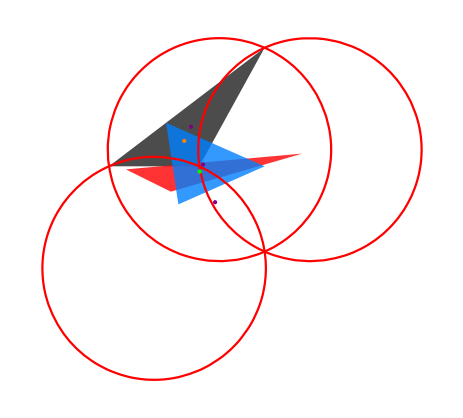

```mathematica
Show[{
drawTriangles[{trg1,evaluate[bPedalTriangle[X[4]]]},ptxa],
{ga[[2]],gb[[2]],gc[[2]]},
Graphics[{PointSize[Medium],Green,Point[evalpt]}],
Graphics[{PointSize[Medium],Orange,Point[evalpt2]}],
Graphics[{PointSize[Medium],Purple,Point[evalpt3]}],
Graphics[{PointSize[Medium],Purple,Point[evalpt4]}],
Graphics[{PointSize[Medium],Purple,Point[evalpt5]}]
}]
```

```mathematica
Show[
{GraficaBaricentricas[c1], GraficaBaricentricas[{x,y,z}.h1]},
drawTriangles[{triangle["K798i"]}],
Graphics[{PointSize[Medium],Green,Point[X[6]//bToCartesianN]}]]
```

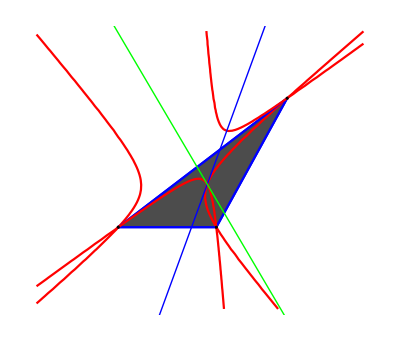

```mathematica
Show[{
drawTriangles[{}],
{GraficaBaricentricas[bCircumconicLEq[X[2],bLine[X[2],X[6]]]//curveSimplify]},
{GraficaBaricentricas[bCircumconicLEq[X[2],bLine[X[2],X[4]]]//curveSimplify]},
Graphics[{Blue,InfiniteLine[{bToCartesianN[X[2]],bToCartesianN[X[6]]}]}],
Graphics[{Green,InfiniteLine[{bToCartesianN[X[2]],bToCartesianN[X[4]]}]}]
}]
```

LOOPING TRIANGLES

```mathematica
Do[
trf=symtr[KimberlingTrianglesBary[trn]];
check=evaluate[bIsParallel[Cross[trf[[2]],trf[[3]]],Cross[xA,bMidpoint[xB,xC]]]]/.rule69//Simplify;
If[check==0,Print[trn]];
,{trn,Keys[KimberlingTrianglesBary]}
];
```

Area or TR / Area of ABC

```mathematica
tr=trgchk;
Det[tr]/(Total[tr[[1]]]Total[tr[[2]]]Total[tr[[3]]])//Simplify
```

(16 (-8 a^6-8 b^6+11 b^4 c^2+11 b^2 c^4-8 c^6+11 a^4 (b^2+c^2)+a^2 (11 b^4+8 b^2 c^2+11 c^4))^2)/((4 a^2+4 b^2-3 c^2)^2 (4 a^2-3 b^2+4 c^2)^2 (3 a^2-4 (b^2+c^2))^2)

```mathematica
((a-b)^2 (a-c)^2 (b-c)^2)/(288(r R)^3)-((a-b)^2 (a-c)^2 (b-c)^2 (a+b+c)^3)/(36 a^3 b^3 c^3)//evaluate//Simplify
```

0